M_α = α(1+α) M

```mathematica
G = (1+α) Subscript[G, N]
```

```mathematica
Exit
```

```mathematica
x1=π/2;
δ[r_,a_,α_] = r^2-2(1+α)(*Subscript[G, N] M*) r +α (1+α)(*M^2*)+a^2;
σ = r^2+ a^2 Cos[x1]^2;
g11[r_,a_,α_]= -δ[r,a,α]/σ+a^2 Sin[x1]^2/σ;
g14[r_,a_,α_] = - a Sin[x1]^2(-δ[r,a,α]+r^2+a^2)/σ;
g22[r_,a_,α_] = σ/δ[r,a,α];
g33[r_,a_]=σ;
g44[r_,a_,α_]=Sin[x1]^2/σ(-a^2 δ[r,a,α] Sin[x1]^2 + (r^2+a^2)^2);
```

## Bh and No bh region

```mathematica
(*
	EXTREMAL CASE FOR HORIZON STRUCTURE AND SPIN-MOG PARAMETERS CHOICES  ! ! !

											a^2 ≤ 1+α   ⇒    |a| ≤ √(1+α)
*)
```

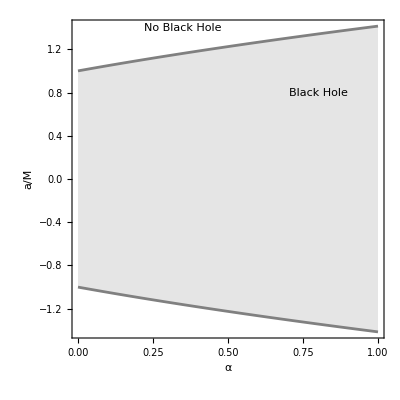

```mathematica
a[l_]=-√(1+l);
tik1=Plot[{-a[l],a[l]},{l,0,1},Filling->Axis,BaseStyle->{12.5,FontFamily->"Times",Italic,Bold},FrameStyle->Black,
Epilog->{Text[Rotate[Framed[Style["Black Hole",FontSize->15,FontColor->GrayLevel[0]],FrameStyle->None,Background->None],0Degree],{0.8,0.8}],Text[Rotate[Framed[Style["No Black Hole",FontSize->15,FontColor->GrayLevel[0]],FrameStyle->None,Background->None],0Degree],{0.35,1.4}]},Frame->True,FrameLabel->{"α","a/M"},PlotStyle->Gray,AspectRatio->1]
```

```mathematica
ll= Table[l,{l,10^-6,1,0.01}];
as = Table[-a[l],{l,10^-6,1,0.01}];
HH = Table[{ll[[i]],as[[i]]},{i,Length[ll]}];
```

```mathematica
Solve[δ[r,a,α]==0&&D[δ[r,a,α],r]==0,{r,a}]
```

{{r→1+α,a→-√(1+α)},{r→1+α,a→√(1+α)}}

```mathematica
Solve[1-(2 M Exp[-a/r])/r==0,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→-a/ProductLog[-a/2]}}

## Horizon radii

```mathematica
(*
													r_± = 1 + α ± √(1-a^2+α)      (Outer and Inner(Cauchy) Horizon)

*)
```

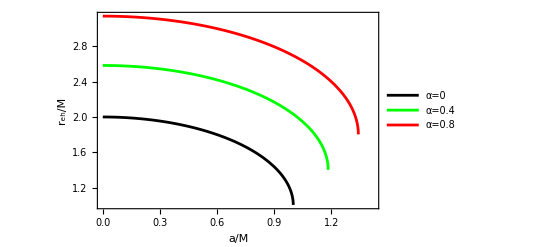

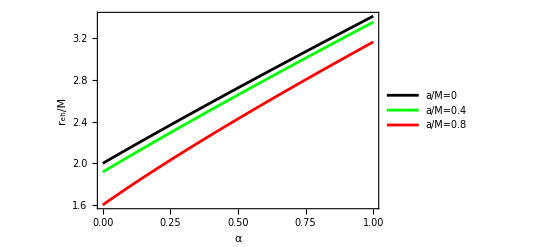

```mathematica
M=1;
rh[a_,α_]=1+α+√(1-a^2+α);

Plot[{rh[a,0],rh[a,0.4],rh[a,0.8]},{a,0,1.42},Frame->True,FrameLabel->{"a/M","r_eh/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α=0","α=0.4","α=0.8"},{Scaled[{0.17,0.2}],{0.5,0.5}}],PlotStyle->{Black,Green,Red}]

Plot[{rh[0,α],rh[0.4,α],rh[0.8,α]},{α,0,1},Frame->True,FrameLabel->{"α","r_eh/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0","a/M=0.4","a/M=0.8"},{Scaled[{0.17,0.6}],{0.5,0.5}}],PlotStyle->{Black,Green,Red}]
```

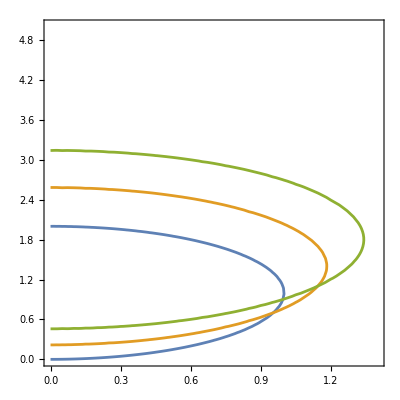

```mathematica
ContourPlot[{δ[r,a,0.0]==0,δ[r,a,0.4]==0,δ[r,a,0.8]==0},{a,0,1.4},{r,0,5}]
```

## isco radii

```mathematica
D[r, r]
```

1

```mathematica
ω= 1/D[g44[r,a,α], r](-D[g14[r,a,α], r] + √((D[g14[r,a,α], r])^2 - (D[g11[r,a,α], r])*(D[g44[r,a,α], r])));

tdot = 1/(√(-g11[r,a,α]-2 ω g14[r,a,α] - ω^2 g44[r,a,α]));

L[r_,a_,α_] = (g14[r,a,α] + ω g44[r,a,α]) tdot;

Lp[r_,a_,α_] = D[L[r,a,α],r];
```

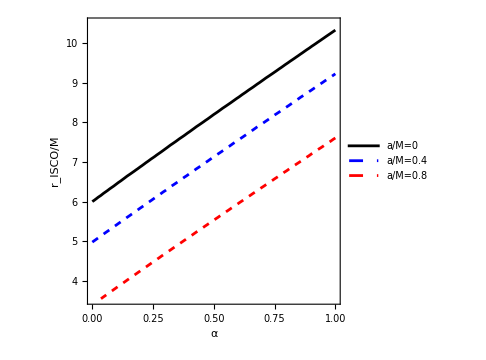

```mathematica
ContourPlot[{Lp[r,0,k]==0,Lp[r,0.3,k]==0,Lp[r,0.7,k]==0},{k,0,1},{r,3.55,10.5(*9.82*)},Frame->True,FrameLabel->{"α","r_ISCO/M"},ImageSize->Medium,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0","a/M=0.4","a/M=0.8"},{Scaled[{0.85,0.15}],{0.5,0.5}}],ContourStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

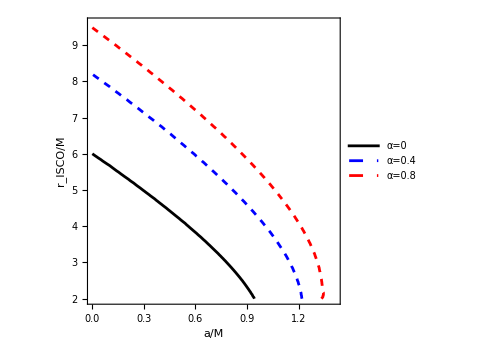

```mathematica
ContourPlot[{Lp[r,a,0]==0,Lp[r,a,0.5]==0,If[(a==0.0445&&r<=4.73),None,Lp[r,a,0.8]]==0},{a,0,√2},{r,2,9.6},Frame->True,FrameLabel->{"a/M","r_ISCO/M"},ImageSize->Medium,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α=0","α=0.4","α=0.8"},{Scaled[{0.85,0.65}],{0.5,0.5}}],ContourStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

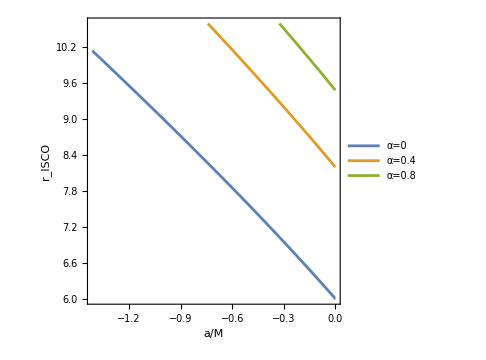

```mathematica
ContourPlot[{Lp[r,a,0]==0,Lp[r,a,0.5]==0,Lp[r,a,0.8]==0},{a,-√2,0},{r,6,10.6},Frame->True,FrameLabel->{"a/M","r_ISCO"},ImageSize->Medium,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α=0","α=0.4","α=0.8"},{Scaled[{0.85,0.65}],{0.5,0.5}}]]
```

## radiative efficiency

```mathematica
Lp[r_,a_,α_] = D[L[r,a,α],r];
Ene[r_,a_,α_] = -(g11[r,a,α]+ω*g14[r,a,α])*tdot;
```

```mathematica
rr1[a_,α_] := r/.FindRoot[Lp[r,a,α]==0,{r,6+0(3.4 α-4 a)}]                     (*ISCO*)
```

```mathematica
η[a_,α_]:=1-Ene[rr1[a,α],a,α]
```

```mathematica
η[0.8,0.1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.77636×10^-15

```mathematica
0.02723869787502564
```

0.0272387

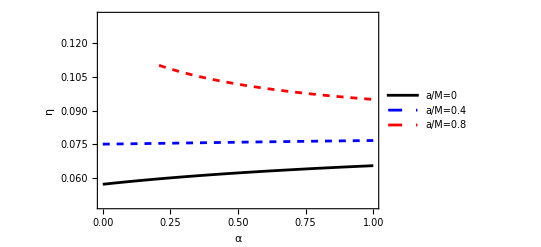

```mathematica
Plot[{η[0,l],η[0.4,l],η[0.8,l]},{l,0.000001,1},Frame->True,FrameLabel->{"α","η"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0","a/M=0.4","a/M=0.8"},{Scaled[{0.82,0.8}],{0.5,0.5}}],PlotRange->{{0,1},{0.048,0.132}},PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

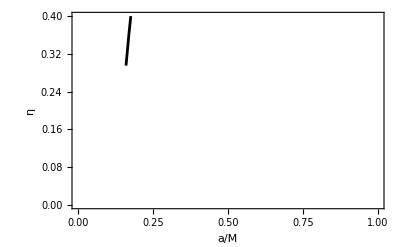

```mathematica
f1=ListLinePlot[Table[{l,1-Ene[r, 1.4, l]/.FindRoot[Lp[r, 1.4, l]==0,{r,0.3}]},{l,0,1,0.01}], PlotRange->{{0, 1},{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

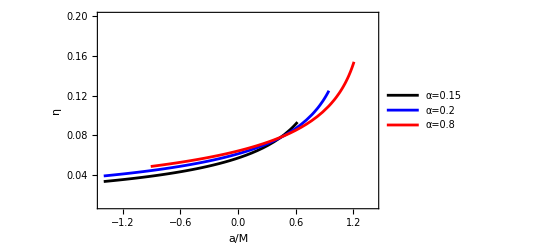

```mathematica
Plot[{η[a,0.],η[a,0.4],If[a<=-0.91,None,η[a,0.8]]},{a,-1.4,1.4},Frame->True,FrameLabel->{"a/M","η"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α=0.15","α=0.2","α=0.8"},{Scaled[{0.2,0.65}],{0.5,0.5}}],PlotRange->{{-1.41,1.41},{0.01,0.2}},PlotStyle->{Black,Blue,Red}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

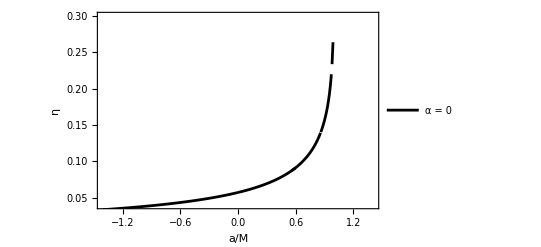

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 10^-6]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,6}]},{a,-1.41,0,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,6}]},{a,0,0.6,0.01}],PlotRange->{{0, 1}{0, 0.4}}, Frame->True,FrameLabel->{"a/M","η"},PlotLegends->Placed[{"α = 0"},{Scaled[{0.13,0.85}], {0.4, 0.5}}],PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f3:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,2.3}]},{a,0.56,0.863,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f4:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,1.75}]},{a,0.863,0.98,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f5:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,1.72}]},{a,0.98,0.99,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f6:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,1.}]},{a,0.99,0.998,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

F1=Show[f1,f2,f3,f4,f5,f6,PlotRange->{{-1.41,1.41},{0.04,0.3}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

```mathematica
m[a_,α_]:=NSolve[Lp[r,a,α]==0,r]
m[0.05,0.1]
```

{{r→6.28126},{r→0.0752585-0.0402287 ⅈ},{r→0.0752585+0.0402287 ⅈ}}

```mathematica
r0[a_, α_]:=r/.First@Select[m[a, α],Im[Last@First@#]==0&]
```

```mathematica
r0[0.5,0.1]
```

4.66592

```mathematica
Plot[r0[a,0.1],{a,0,1}]
```

$Aborted

```mathematica
Eisco[a_,α_]:=Ene[r0[a,α],a,α]
```

```mathematica
n[a_,α_]:=If[1-Eisco[a,α]>=0,1-Eisco[a,α],None]
```

```mathematica
Plot[n[a,0],{a,-√2,√2}]
```

```mathematica
n[1.01,0]
```

1.33672

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

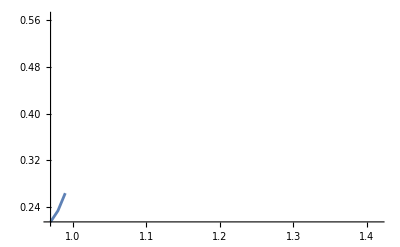

```mathematica
ListLinePlot[Table[{a,n[a,0]},{a,0.9,√2,0.01}],PlotRange->{{0.97,√2},{0.214945,0.565999}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

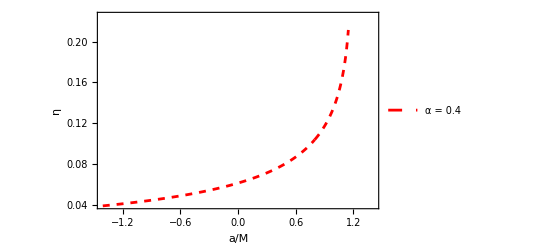

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 0.4]/.FindRoot[Lp[r, a, 0.4]==0,{r,5.5}]},{a,-1.41,0.8,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Red,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.4]/.FindRoot[Lp[r, a, 0.4]==0,{r,3}]},{a,0.8,1.2,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Red,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f3:=ListLinePlot[Table[{a,1-Ene[r, a, 0.4]/.FindRoot[Lp[r, a, 0.4]==0,{r,1.4}]},{a,1.2,1.3,0.01}],PlotLegends->Placed[{"α = 0.4"},{Scaled[{0.13,0.7}], {0.4, 0.5}}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Red,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f4:=ListLinePlot[Table[{a,1-Ene[r, a, 0.4]/.FindRoot[Lp[r, a, 0.4]==0,{r,0.9}]},{a,1.3,1.41,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Red,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

F2=Show[f1,f2,f3,f4,PlotRange->{{-1.41,1.41},{0.04,0.225}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

General::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListLinePlot,#1,#2]&,{{{0,0.4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

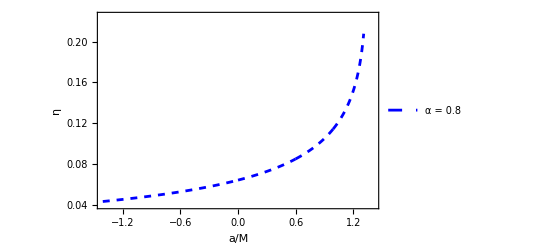

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 0.8]/.FindRoot[Lp[r, a, 0.8]==0,{r,9}]},{a,-1.41,0.,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Blue,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.8]/.FindRoot[Lp[r, a, 0.8]==0,{r,8}]},{a,0,0.6,0.01}], PlotLegends->Placed[{"α = 0.8"},{Scaled[{0.13,0.55}], {0.4, 0.5}}],PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Blue,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f3:=ListLinePlot[Table[{a,1-Ene[r, a, 0.8]/.FindRoot[Lp[r, a, 0.8]==0,{r,7}]},{a,0.6,0.99,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Blue,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

f4:=ListLinePlot[Table[{a,1-Ene[r, a, 0.8]/.FindRoot[Lp[r, a, 0.8]==0,{r,4}]},{a,0.99,1.41,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Blue,Dashed},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

F3=Show[f1,f2,f3,f4,PlotRange->{{-1.41,1.41},{0.04,0.225}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

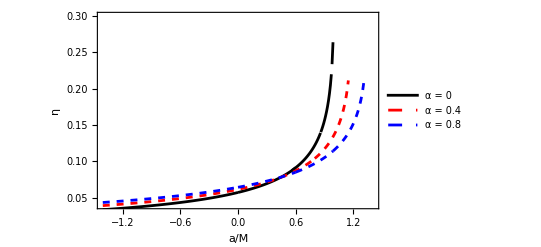

```mathematica
Show[F1,F2,F3]
```

```mathematica
rr1[0.,0.000001]
```

6.

## Jet

```mathematica
<<MaTeX`;
```

```mathematica
Wh[a_,α_]:= (-g14[r,a,α])/g44[r,a,α]/.{r->1+α+√(1-a^2+α)}
```

```mathematica
Wh[-0.99,0.]
```

-0.433804

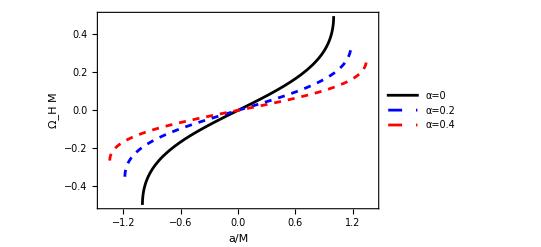

```mathematica
Plot[{Wh[a,0],Wh[a,0.4],Wh[a,0.8]},{a,-√2,√2},Frame->True,FrameLabel->{"a/M","Ω_H M"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α=0","α=0.2","α=0.4"},{Scaled[{0.8,0.2}],{0.5,0.5}}],PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

```mathematica
Plot[{Wh[0.1,k],Wh[0.2,k],Wh[0.4,k]},{k,0,1},Frame->True,FrameLabel->{"MaTeX[\\alpha]",MaTeX[\\Omega_{H} M]},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0.1","a/M=0.2","a/M=0.8"},{Scaled[{0.8,0.6}],{0.5,0.5}}],PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

```mathematica
LogK2min = Log[10](2.94-0.22); LogK2 =Log[10]( 2.94); LogK2max = Log[10](2.94+0.22);
LogK5min = Log[10](4.19-0.22);LogK5 =Log[10]( 4.19); LogK5max = Log[10](4.19+0.22);
```

## A0620-00 (JET)

```mathematica
P2=0.13; P5=1.6;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.04}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.04}]//Quiet

data2min=ParallelTable[{l, a2min[l]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, a5min[l]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

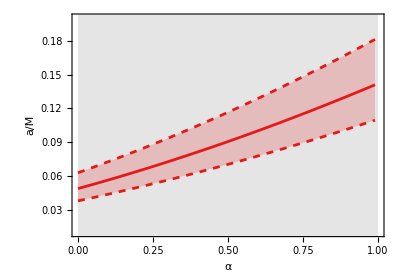

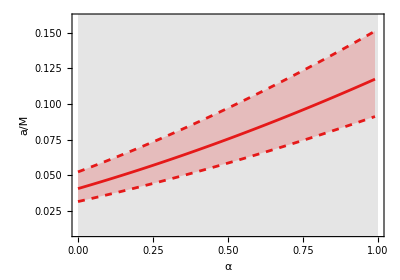

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.01,0.2}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.01,0.16}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","A0620 - 00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

```mathematica
a2max[1]
```

0.110385

## H1743-322

```mathematica
Clear[P2,P5,a2max,a2,a2min,a5max,a5,a5min]
```

```mathematica
P2=7;P5=140;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.4}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.4}]//Quiet

data2min=ParallelTable[{l, a2min[l]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, a5min[l]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

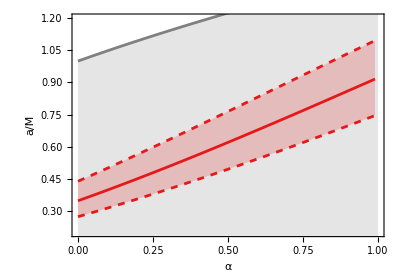

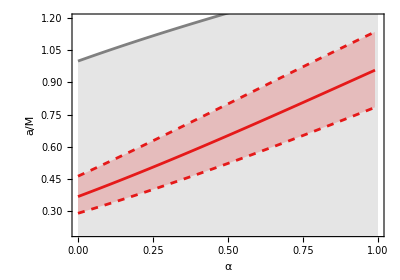

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.2,1.2}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.2,1.2}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## XTEJ1550-564

```mathematica
Clear[P2,P5,a2max,a2,a2min,a5max,a5,a5min]
```

```mathematica
P2=11;P5=180;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.4}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.4}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.4}]//Quiet

data2min=ParallelTable[{l, a2min[l]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, a5min[l]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

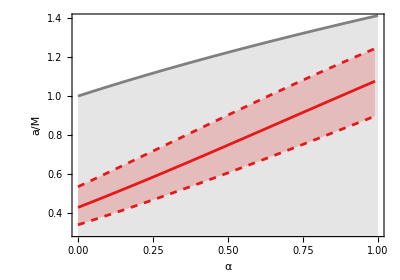

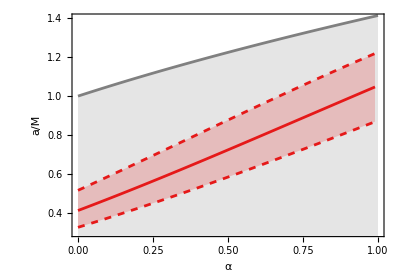

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.3,1.4}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.3,1.4}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## GRS1124-683

```mathematica
P2=3.9;P5=380;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.28}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.28}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.28}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.58}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.58}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.58}]//Quiet

data2min=ParallelTable[{l, a2min[l]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, a5min[l]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

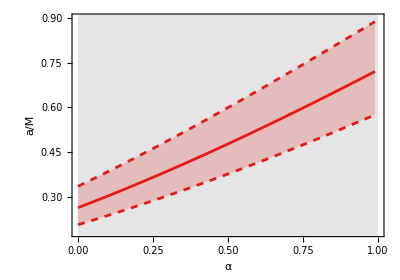

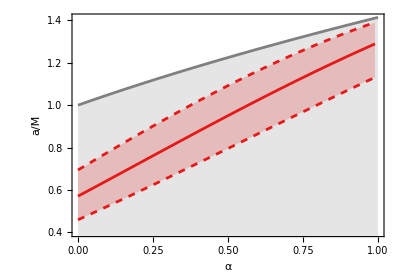

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.18,0.9}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.4,1.41}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## GROJ1655-40

```mathematica
P2=70;P5=1600;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.85}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.85}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.85}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.91}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.91}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.91}]//Quiet

data2min=ParallelTable[{l, If[l>=0.36,-a[l],a2min[l]]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, If[l>=0.2,-a[l],a5min[l]]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

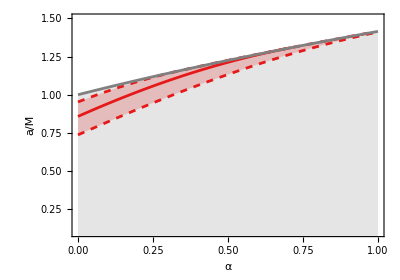

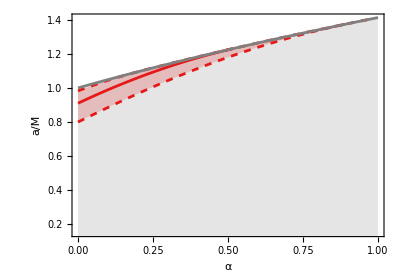

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.1,1.5}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.15,1.41}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","GROJ1655-40"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","GROJ1655-40"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## GRS 1915+105

```mathematica
P2=42;P5=660;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.7}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.7}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.7}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.75}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.75}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.75}]//Quiet

data2min=ParallelTable[{l, If[l>=0.71,-a[l],a2min[l]]}, {l, 10^-7,1, 0.01}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,1, 0.01}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,1, 0.01}];

data5min=ParallelTable[{l, If[l>=0.8,-a[l],a5min[l]]}, {l, 10^-7,1, 0.01}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,1, 0.01}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,1, 0.01}];
```

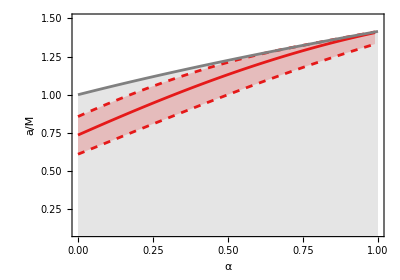

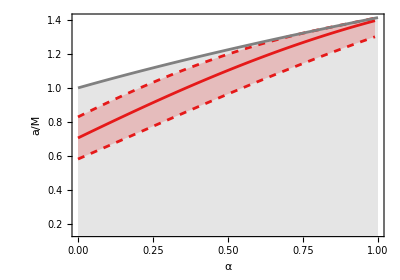

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.1,1.5}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,1},{0.15,1.41}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α","a/M","Γ = 2","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α","a/M","Γ = 5","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## Efficiency

### A0620-00

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
η1=0.054;η2=0.061;η3=0.07;
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5},{a,0.02}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5},{a,0.02}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&&1-Ene[r,a,l]==η3},{{r,6},{a,0.06-0.12/0.76 l}}]
```

```mathematica
dat1:=Table[{l,amin[l]},{l,10^-6,1,0.01}];
dat2:=Table[{l,aa[l]},{l,10^-6,1,0.01}];
dat3:=Table[{l,amax[l]},{l,10^-6,1,0.01}];
```

```mathematica
amin[0]
```

-0.106654

```mathematica
s1=Plot[{(*-0.05-0.13/0.544 l,0.06-0.09/0.51 l,0.19-0.08/0.77 l*)-0.107-(0.447-0.107)/0.646 l,0.11-(0.11+0.091)/0.633 l,0.312-(0.312-0.192)/0.925 l},{l,0,1},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","A0620-00"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

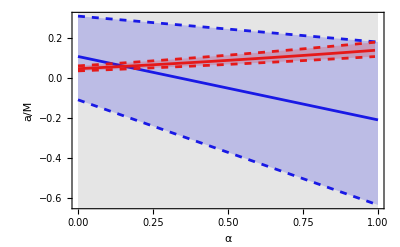

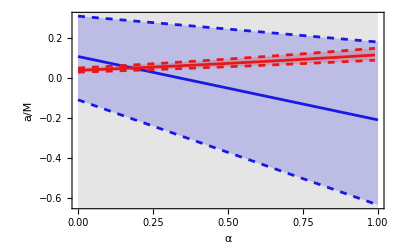

```mathematica
Show[s1,p1,tik1,FrameLabel->{"α","a/M","Γ = 2","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s1,p2,tik1,FrameLabel->{"α","a/M","Γ = 5","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}](*with reg.Plot*)
```

### H1743-322

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
η1=0.065-0.011;η2=0.065;η3=0.065+0.017;
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5.6},{a,0.3}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.6},{a,0.3}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,5.6},{a,0.3}}]//Quiet
```

```mathematica
s2=Plot[{amin[l],aa[l],amax[l]},{l,0.00001,1},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","H1743-322"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

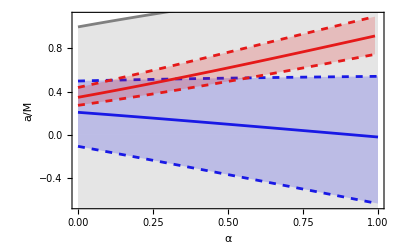

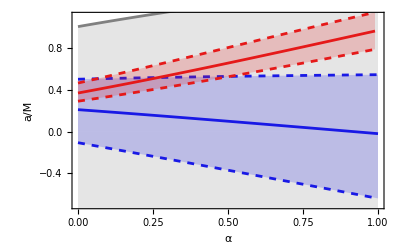

```mathematica
Show[s2,p1,tik1,FrameLabel->{"α","a/M","Γ = 2","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{-0.65,1.1}}]
Show[s2,p2,tik1,FrameLabel->{"α","a/M","Γ = 5","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{-0.7,1.1}}]
```

### XTE J1550-564

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
η1=0.072-0.011;η2=0.072;η3=0.072+0.017;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5.6},{a,0.5}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.6},{a,0.5}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,5.6},{a,0.5}}]//Quiet
```

```mathematica
s3=Plot[{(*0.07+(0.04-0.03)/(0.08-0.186) l,0.23+(0.21-0.2)/(0.038-0.11) l,0.523+(0.436-0.523) l*)amin[l],aa[l],amax[l]},{l,0.,1},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","XTEJ1550-564"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

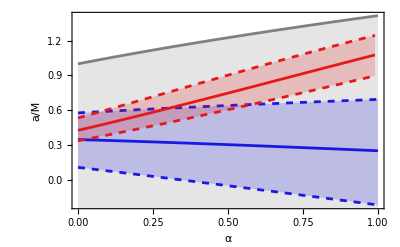

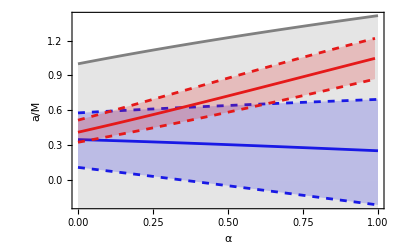

```mathematica
Show[s3,p1,tik1,FrameLabel->{"α","a/M","Γ = 2","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{-0.213,1.41}}]
Show[s3,p2,tik1,FrameLabel->{"α","a/M","Γ = 5","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{-0.213,1.41}}]
```

### GRS1124-683

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.095-0.017;η2=0.095;η3=0.095+0.025;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,7},{a,0.8}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.5},{a,0.8}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,7},{a,0.8}}]//Quiet
```

```mathematica
s4=Plot[{(*0.282+(0.26-0.25)/(0.689-1) l,0.49+(0.57-0.52)l,0.52+(1.05-0.52) l*)amin[l],aa[l],amax[l]},{l,0,1},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},(*PlotRange->{{10^-6,0.02},{0.,0.82}},*) Frame->True,FrameLabel->{"α/M^2","a/M","GRS1124-683"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

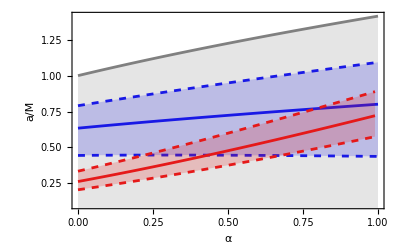

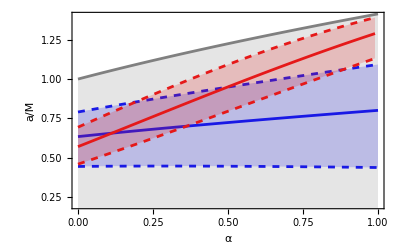

```mathematica
Show[s4,p1,tik1,FrameLabel->{"α","a/M","Γ = 2","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{0.1,√2}}]
Show[s4,p2,tik1,FrameLabel->{"α","a/M","Γ = 5","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold},PlotRange->{{0,1},{0.2,1.4}}]
```

### GROJ1655-40

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.104-0.013;η2=0.104;η3=0.104+0.018;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,6},{a,0.793}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5},{a,0.706}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,6},{a,0.8}}]//Quiet
```

```mathematica
ef1 = ParallelTable[{l,amin[l]},{l,10^-6,1,0.01}];
ef2 = ParallelTable[{l,aa[l]},{l,10^-6,1,0.01}];
ef3 = ParallelTable[{l,amax[l]},{l,10^-6,1,0.01}];
```

```mathematica
s5=Plot[{(*0.48-(0.475-0.47)/(1-0.61) l,0.523+(0.716-0.523) l,0.6+(0.99-0.523)l*)amin[l],aa[l],amax[l]},{l,0,1},(*,PlotRange->{{0.,0.02},{0.1,1.01}}*)AspectRatio->0.7,  PlotStyle->{{Blue, Dashed},Blue, {Blue, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];

(*s5=ListLinePlot[{ef1,ef2,ef3},Joined->True, InterpolationOrder->1(*,PlotRange->{{0.,0.02},{0.1,1.01}}*),AspectRatio->0.7,  PlotStyle->{{Blue, Dashed},Blue, {Blue, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]]*)
```

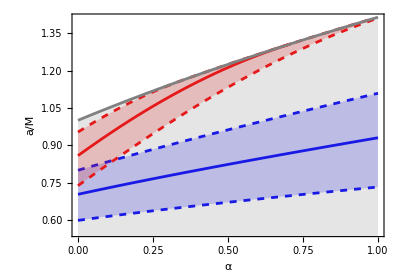

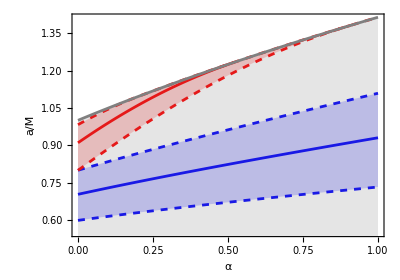

```mathematica
Show[{s5,p1,tik1},FrameLabel->{"α","a/M", "Γ = 2", "GROJ1655-40"},PlotRange->{{0,1},{0.55,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[{s5,p2,tik1},FrameLabel->{"α","a/M", "Γ = 5", "GROJ1655-40"},PlotRange->{{0,1},{0.55,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

### GRS 1915+105

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.234;η2=0.234+0.014;η3=0.234+0.028;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,6},{a,0.999}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,6},{a,0.999}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,6},{a,0.999}}]//Quiet
```

```mathematica
d1=ParallelTable[{l,(*0.52+(0.559-0.522)/0.082 l*)amin[l]},{l,10^-6,1,0.01}];
d2=ParallelTable[{l,aa[l](*0.522+(0.735-0.522)/0.442 l*)},{l,10^-6,1,0.01}];
d3=ParallelTable[{l,amax[l](*0.524+(0.742-0.522)/0.448 l*)},{l,10^-6,1,0.01}];
s6=ListLinePlot[{d1,d2,d3},Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.8},{0.1,1.41}},AspectRatio->0.7,  PlotStyle->{{Blue, Dashed},Blue, {Blue, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
```

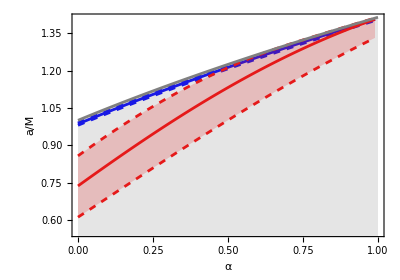

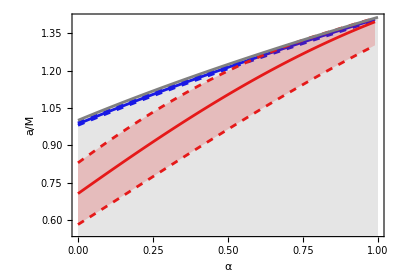

```mathematica
Show[{s6,p1,tik1},Epilog->{Inset[Γ2zoom,Scaled[{0.68,0.3}]]},FrameLabel->{"α","a/M", "Γ = 2", "GRS 1915+105"},PlotRange->{{0,1},{0.55,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[{s6,p2,tik1},Epilog->{Inset[Γ5zoom,Scaled[{0.68,0.3}]]},FrameLabel->{"α","a/M", "Γ = 5", "GRS 1915+105"},PlotRange->{{0,1},{0.55,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

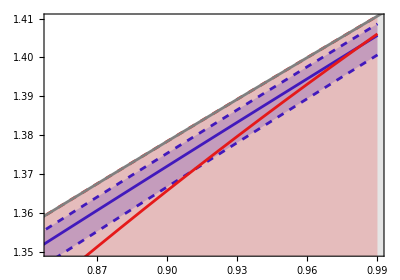

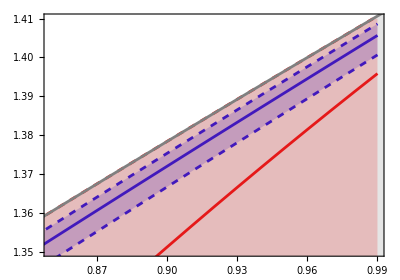

```mathematica
Γ2zoom=Show[{s6,p1,tik1},(*FrameLabel->{"α","a/M", "Γ = 2", "GRS 1915+105"},*)PlotRange->{{0.85,0.99},{1.35,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Γ5zoom=Show[{s6,p2,tik1}(*,FrameLabel->{"α","a/M", "Γ = 5", "GRS 1915+105"}*),PlotRange->{{0.85,0.99},{1.35,1.41}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## veff(r) .

```mathematica
x = g44[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
y = g14[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
z = g11[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
```

```mathematica
A = (-g11[r,a,α])/g22[r,a,α] x^2-g44[r,a,α]/g22[r,a,α] y^2 + 2 g14[r,a,α]/g22[r,a,α] x y;
B = x L y g11[r,a,α]/g22[r,a,α] + y z L g44[r,a,α]/g22[r,a,α] - g14[r,a,α]/g22[r,a,α]*(x L z + y^2 L);
Csq = (-g44[r,a,α])/g22[r,a,α] L^2 z^2 + 2 g14[r,a,α]/g22[r,a,α] L^2 y z - 1/g22[r,a,α];
```

```mathematica
Clear[Vpl]
```

```mathematica
Vpl[r_,a_,α_,L_] = B/A + √(B^2 - A Csq);
```

```mathematica
Vmn[r_,a_,α_,L_] = B/A - √(B^2 - A Csq);
```

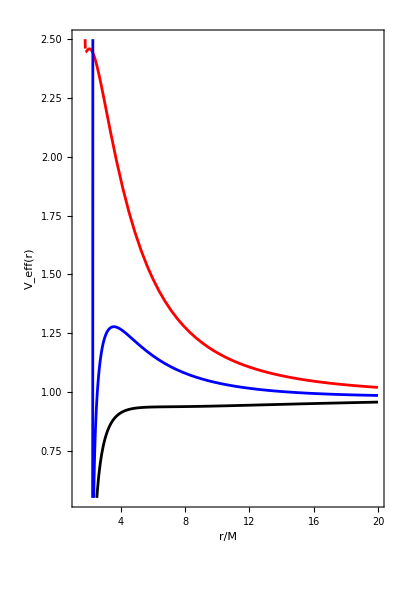

```mathematica
Plot[{Vpl[r,0,0.2,4],Vpl[r,0.8,0.12,6],Vpl[r,0.1,0.2,6]},{r,1.5,20},Frame->True,FrameLabel->{"r/M","V_eff(r)"},PlotStyle->{Black,Red,Blue},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 17},AspectRatio->1.5,PlotRange->{{1.35,20},{0.55,2.5}}]
```

```mathematica
Solve[D[Vpl[]]]
```

```mathematica
Vpl[r,a,α,L];
```

```mathematica
Limit[Vpl[r,a,α,L],r->Infinity]
```

1

```mathematica
Limit[Vmn[r,a,α,L],r->Infinity]
```

-1

```mathematica
Solve[{D[Vpl[r,a,α,L],r]==0 ,D[ Vpl[r,a,α,L],r,r]==0},{r,L}][[1]]
```

$Aborted

```mathematica
Vpl[r,0.4,0.1,L]//FullSimplify
```

(L (0.0108112+r (-0.248679+r (2.25545+r (-10.6243+r (29.287+r (-49.7607+r (51.1725+r (-35.4112+r (20.792+r (-8.8+1.6 r)))))))))))/(-0.000553133+r (0.0209558+r (-0.25504+r (1.33348+r (-3.28062+r (3.86278+r (1.66416+r (-9.30688+r (16.2825+r (-12.804+r (8.1+r (-4.4+1. r))))))))))))+√((-2.02348×10^-6+r (0.000132556+r (-0.0036901+L^2 (0.000113026+r (-0.00508389+r (0.101373+r (-1.19184+r (9.30511+r (-51.7133+r (214.586+r (-687.719+r (1742.92+r (-3555.9+r (5930.97+r (-8222.44+r (9625.53+r (-9591.99+r (8063.72+r (-5702.44+r (3421.24+r (-1721.83+r (704.421+r (-231.+r (59.99+(-11.+r) r)))))))))))))))))))))+r (0.0589123+r (-0.610401+r (4.39409+r (-22.941+r (89.2408+r (-261.842+r (575.987+r (-912.314+r (883.644+r (23.7951+r (-2008.72+r (4595.87+r (-6845.08+r (7922.09+r (-7602.89+r (6185.79+r (-4301.68+r (2581.03+r (-1326.71+r (572.299+r (-204.248+r (57.59+(-11.+r) r)))))))))))))))))))))))))/(r^2 (0.1164+r (-1.13344+r (3.424+r (-5.632+r (2.83+(-2.2+r) r)))))^4))

```mathematica
Solve[Vpl[r,0.4,0.1,L]==0,L]
```

$Aborted

```mathematica
(*Effektiv potensialni har xil L uchun chizib ko'rish*)Manipulate[Plot[Vpl[r,L,0.5,0.1],{r,2,20},PlotRange->All,AxesLabel->{"r","Veff"},GridLines->Automatic,PlotLabel->Style["Effektiv potensial",14,Bold],Epilog->{Red,PointSize[0.02],Point[{r/. solution,Vpl[r/. solution,L/. solution,0.5,0.1]}]}],{L,2,10}]
```